```mathematica
Directory[]
```

/Users/stevenredford

```mathematica
SetDirectory["/Users/stevenredford/afines/AFINES/out2/"];
```

```mathematica
actin5 = pts2["/Users/stevenredford/afines/AFINES/out2", "actins"];
```

```mathematica
link5 =  pts2["/Users/stevenredford/afines/AFINES/out2", "links"];
```

```mathematica
placeholder = draw[actin5, link5, "", "", "", False, {10, 10}, True, 35];
```

```mathematica
nframes = Length[placeholder]
```

101

```mathematica
ListAnimate[placeholder]
```

```mathematica
order = nemt[link5, "", {10,10}];
```

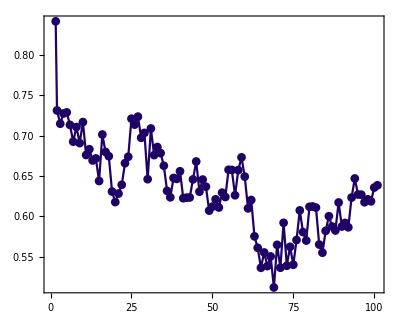

```mathematica
ListPlot[order]
```